Lf  is the length of a single frame section
Lc is the length of the cross-slide

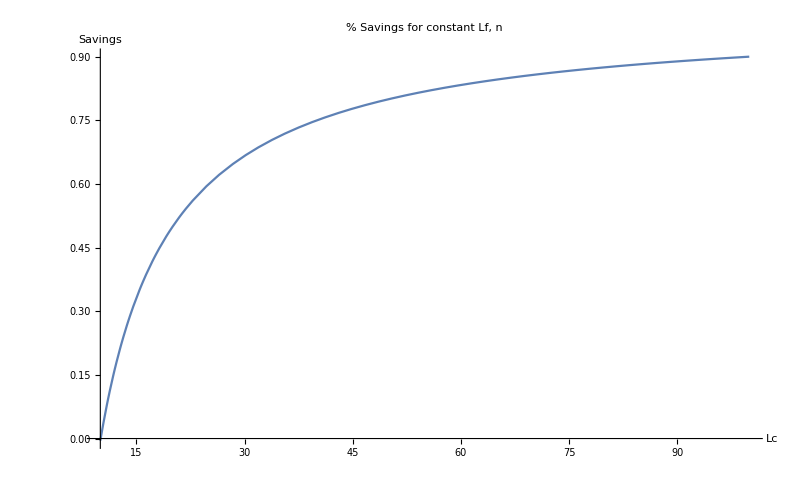

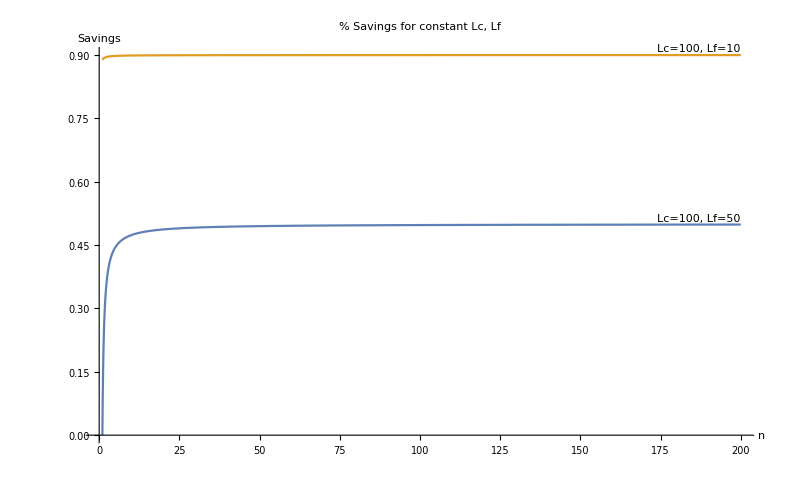

```mathematica
AffordableFrame[Lc_, Lf_, n_, costPerMeter_,height_, x_]:= Module[{
workspaceLength = n* Lc -Lf ,
totalLength = n* Lc  
(*totalSavings = n(Lc - Lf) - Lf *)
},{
totalSavings  = workspaceLength - n Lf; (*n* Lc -Lf -n Lf = n Lc - (n+1)Lf*)
graphicsList = Table[{
Black, Rectangle[{-(Lc- Lf),0}, {totalLength, height}]
},{i,0,n + 2-1}];
graphicsList[[2]] = {Cyan, Rectangle[{x-(Lc- Lf),2*height}, {x-(Lc- Lf)+Lc, 3*height}]};
counter = 1;
For[i=3,i<=n+2, i++,
graphicsList[[i]] = {Red,Rectangle[{(counter-1)*Lc,height}, {(counter-1)*Lc+Lf, 2*height}]};
counter += 1
];
totalLength,
workspaceLength,
totalSavings,
Graphics[
graphicsList
],
(n Lc - (n+1)Lf)/(n* Lc -Lf),
graphicsList;
}]

Plot[AffordableFrame[Lcc, 10, 200, 1000, 40, 0][[5]],{Lcc,10,100},PlotLabel->"% Savings for constant Lf, n", AxesLabel->{"Lc", "Savings"}]
Plot[{AffordableFrame[ 100,50, nn, 1000, 40, 0][[5]],AffordableFrame[ 100,10, nn, 1000, 40, 0][[5]]},{nn,1,200}, AxesOrigin->{0,0}, PlotLabel->"% Savings for constant Lc, Lf", AxesLabel->{"n", "Savings"}, PlotLabels->Placed[{"Lc=100, Lf=50","Lc=100, Lf=10","local x"},Above]]
Manipulate[
Animate[AffordableFrame[Lcc, 10, nn, 1000, 40, t][[4]]
,{t,0,(nn-1)*Lcc+(Lcc-10),Appearance->"Labeled"},Initialization:>{t=0}, AnimationRunning->False, AnimationDirection->ForwardBackward],{Lcc,11,100},{nn, 1,200}]
```